## Experimenting

```mathematica
Map[#[EntityProperty["AdministrativeDivision","StateAbbreviation"]]&,EntityList[EntityClass["AdministrativeDivision","AllUSStatesPlusDC"]]]
```

{AL,AK,AZ,AR,CA,CO,CT,DE,DC,FL,GA,HI,ID,IL,IN,IA,KS,KY,LA,ME,MD,MA,MI,MN,MS,MO,MT,NE,NV,NH,NJ,NM,NY,NC,ND,OH,OK,OR,PA,RI,SC,SD,TN,TX,UT,VT,VA,WA,WV,WI,WY}

```mathematica
stateLinks = Import["https://publicreporting.sts.org/chsd?title=&field_state_value=NY", "Hyperlinks"]
```

{https://publicreporting.sts.org//,http://www.sts.org/,https://publicreporting.sts.org/search/acsd,https://publicreporting.sts.org/acsd-exp,https://publicreporting.sts.org/chsd-exp,https://publicreporting.sts.org/gtsd,https://publicreporting.sts.org/gtsd-exp,https://publicreporting.sts.org/resources,https://publicreporting.sts.org/consent-forms,http://www.sts.org/media/sts-public-reporting-toolkit/frequently-asked-questions-and-answers-about-sts-national-database-and-public-reporting,http://www.sts.org/public-reporting-glossary,http://www.sts.org/media/sts-public-reporting-toolkit,https://publicreporting.sts.org/additional-info,https://publicreporting.sts.org/contact,https://ctsurgerypatients.org/,https://publicreporting.sts.org/congenital/50127,https://publicreporting.sts.org/congenital/50119,https://publicreporting.sts.org/congenital/50075,https://publicreporting.sts.org/congenital/50063,https://publicreporting.sts.org/congenital/50097,https://publicreporting.sts.org/congenital/50006,https://publicreporting.sts.org/congenital/50082,http://www.sts.org/misc/notice-and-disclaimer,http://www.sts.org/sts-privacy-statement}

```mathematica
hospName = Import["https://publicreporting.sts.org/chsd?title=&field_state_value=NY", "Data"]
```

{{Explanation of Star Ratings,Congenital Heart,Explanation of Star Ratings,{Consent Forms,FAQs,Glossary,Toolkit,Additional Info,Contact},Patient Information},{Name,{Albany Medical Center Albany, New York ,Cohen Children's Medical Center of New York New Hyde Park, New York ,Hassenfeld Children's Hospital at NYU Langone New York, New York ,Montefiore Medical Center & Albert Einstein College of Medicine New York, New York ,Mount Sinai Hospital New York, New York ,New York Presbyterian / Morgan Stanley Children's Hospital New York, New York ,University of Rochester Medical Center Rochester, New York }}}

```mathematica
hospName[[2]][[2]][[1]]
```

Albany Medical Center Albany, New York

```mathematica
stateFacLinks = Select[stateLinks, StringContainsQ[#, "congenital"]&]
```

{https://publicreporting.sts.org/congenital/50127,https://publicreporting.sts.org/congenital/50119,https://publicreporting.sts.org/congenital/50075,https://publicreporting.sts.org/congenital/50063,https://publicreporting.sts.org/congenital/50097,https://publicreporting.sts.org/congenital/50006,https://publicreporting.sts.org/congenital/50082}

```mathematica
stateLocs  =  Import["https://publicreporting.sts.org/chsd?title=&field_state_value=NY", "Data"]
```

{{Explanation of Star Ratings,Congenital Heart,Explanation of Star Ratings,{Consent Forms,FAQs,Glossary,Toolkit,Additional Info,Contact},Patient Information},{Name,{Albany Medical Center Albany, New York ,Cohen Children's Medical Center of New York New Hyde Park, New York ,Hassenfeld Children's Hospital at NYU Langone New York, New York ,Montefiore Medical Center & Albert Einstein College of Medicine New York, New York ,Mount Sinai Hospital New York, New York ,New York Presbyterian / Morgan Stanley Children's Hospital New York, New York ,University of Rochester Medical Center Rochester, New York }}}

```mathematica
tool=LLMTool[{"getCity","Get a city from a string"},"city"->"City",Slot["city"]["Population"]&];
req=LLMToolRequest["cityPopulationFinder",{"city"->"Chicago"}];
```

```mathematica
stateXML  =  Import["https://publicreporting.sts.org/chsd?title=&field_state_value=NY", "XMLObject"];
```

```mathematica
stateLocs[[2]][[3]];
```

```mathematica
FirstCase[stateLocs[[2]][[3]],  XMLElement["div",{"class"->"search--location"},{"Albany, New York"}]]
```

Missing[NotFound]

```mathematica
stateLocXML = Cases[stateXML,  XMLElement["div",{"class"->"search--location"},{_String}],  Infinity]
```

{XMLElement[div,{class→search--location},{Albany, New York}],XMLElement[div,{class→search--location},{New Hyde Park, New York}],XMLElement[div,{class→search--location},{New York, New York}],XMLElement[div,{class→search--location},{New York, New York}],XMLElement[div,{class→search--location},{New York, New York}],XMLElement[div,{class→search--location},{New York, New York}],XMLElement[div,{class→search--location},{Rochester, New York}]}

```mathematica
locs = Last[Last[#]]&/@ stateLocXML
```

{Albany, New York,New Hyde Park, New York,New York, New York,New York, New York,New York, New York,New York, New York,Rochester, New York}

```mathematica
ResourceFunction["DarkMode"][]
```

Albany

```mathematica
GeoLocation["Albany, NY"]
```

GeoLocation[Albany, NY]

```mathematica
tool=LLMTool["getCity","string",Interpreter["City"][#]&]
```

LLMTool[…]

```mathematica
LLMSynthesize["Get the \"City, State\" from the following input: Albany Medical Center Albany, New York"]
```

Albany, New York

```mathematica
"Albany Medical Center Albany, New York"
```

Albany Medical Center Albany, New York

```mathematica
StringCases["Albany Medical Center Albany, New York",WordCharacter..]
```

{Albany,Medical,Center,Albany,New,York}

```mathematica
GeoLocation[%]
```

GeoLocation[Albany, New York]

```mathematica
LLMSynthesize["Find the city in Albany Medical Center Albany, New York and plug it into the tool.",LLMEvaluator-><|"Tools"->tool|>]
```

It seems that the tool was not able to interpret the city from the given input. Let's try again by providing a simpler input.

```mathematica
i = Interpreter["Location"]
```

Interpreter[Location]

```mathematica
i[stateLocs[[2]][[2]][[6]]]
```

Failure[…]

```mathematica
SemanticInterpretation[stateLocs[[2]][[2]][[1]]]
```

$Failed

```mathematica
i[stateLocs[[2]][[2]][[5]]]
```

Failure[…]

```mathematica
g = FindGeoLocation[stateLocs[[2]][[2]][[5]]]
```

GeoPosition[{40.79,-73.9531}]

```mathematica
GeoGraphics[g]
```

-Graphics-

Failure[…]

```mathematica
stateData = Import["https://publicreporting.sts.org/congenital/50127", "Elements"]
```

{Data,FullData,Hyperlinks,ImageLinks,Images,Plaintext,Source,Summary,Title,XMLObject}

```mathematica
title = Import["https://publicreporting.sts.org/congenital/50127", "Title"]
```

Albany Medical Center | STS Public Reporting

```mathematica
stateData = Import["https://publicreporting.sts.org/congenital/50127", "Plaintext"]
```

Skip to main content   
 
   
 
 
 
  STS Public Reporting      
 
 

            
 
 
 
 
Adult Cardiac
Explanation of Star Ratings Congenital Heart General Thoracic
Explanation of Star Ratings Resources
Consent Forms FAQs Glossary Toolkit Additional Info Contact Patient Information      
 
   
 
     
                   
 
 
 

 
 

 
  Albany Medical Center    Albany, New York  
 
 
NOTE: Results are based on a participant’s unique group of patients (known as case mix) and the number of surgical procedures in each category. Results published are specific to the participant listed and are not intended for direct comparison to other participants.  
 
For this Congenital Heart Surgery Database (CHSD) participant, rating is based on the overall observed-to-expected operative mortality ratio for all patients undergoing pediatric and/or congenital cardiac surgery.  
Participant is enrolled in public reporting for the Congenital Heart Surgery Database but did not receive analysis results for the current timeframe (July 2019 - June 2023).  
   
 

 
   
 
         
   
Operative and Adjusted Operative Mortality (July 2019-June 2023)  
Population: Neonates, Infants, Children & Adults # / Eligible Observed Expected O/E Ratio (95% CI) Adj. Rate (95% CI)  
Overall  2 / 248 0.81% 1.71% 0.47 (0, 1.21) 1.25 (0, 3.21)
STAT Mortality Category 1  0 / 162 0% 0.57% 0 (0, 3.94) 0 (0, 2.54)
STAT Mortality Category 2  1 / 45 2.22% 1.44% 1.55 (0.04, 8.19) 3 (0.08, 15.91)
STAT Mortality Category 3  1 / 13 7.69% 3.5% 2.2 (0.06, 10.31) 7.36 (0.19, 34.46)
STAT Mortality Category 4  0 / 20 0% 5.65% 0 (0, 2.98) 0 (0, 23.34)
STAT Mortality Category 5  0 / 8 0% 13.55% 0 (0, 2.73) 0 (0, 40.8)      
 
   
           
 
 
 
 

      
 
 

Copyright © 2020 The Society of Thoracic Surgeons. All rights reserved. Expanded Proprietary Notice and Disclaimer and STS Privacy Statement .

```mathematica
stateData
```

{{Explanation of Star Ratings,Congenital Heart,Explanation of Star Ratings,{Consent Forms,FAQs,Glossary,Toolkit,Additional Info,Contact},Patient Information},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{{Overall,2 / 248,0.81%,1.71%,0.47 (0, 1.21),1.25 (0, 3.21)},{STAT Mortality Category 1,0 / 162,0%,0.57%,0 (0, 3.94),0 (0, 2.54)},{STAT Mortality Category 2,1 / 45,2.22%,1.44%,1.55 (0.04, 8.19),3 (0.08, 15.91)},{STAT Mortality Category 3,1 / 13,7.69%,3.5%,2.2 (0.06, 10.31),7.36 (0.19, 34.46)},{STAT Mortality Category 4,0 / 20,0%,5.65%,0 (0, 2.98),0 (0, 23.34)},{STAT Mortality Category 5,0 / 8,0%,13.55%,0 (0, 2.73),0 (0, 40.8)}}}}

```mathematica
Map[Length,%315]
```

{5,2}

```mathematica
Length[stateData]
```

2

```mathematica
header = stateData[[2]][[1]]
```

{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)}

```mathematica
body = Join[stateData[[2]][[2]]]
```

{{Overall,2 / 248,0.81%,1.71%,0.47 (0, 1.21),1.25 (0, 3.21)},{STAT Mortality Category 1,0 / 162,0%,0.57%,0 (0, 3.94),0 (0, 2.54)},{STAT Mortality Category 2,1 / 45,2.22%,1.44%,1.55 (0.04, 8.19),3 (0.08, 15.91)},{STAT Mortality Category 3,1 / 13,7.69%,3.5%,2.2 (0.06, 10.31),7.36 (0.19, 34.46)},{STAT Mortality Category 4,0 / 20,0%,5.65%,0 (0, 2.98),0 (0, 23.34)},{STAT Mortality Category 5,0 / 8,0%,13.55%,0 (0, 2.73),0 (0, 40.8)}}

```mathematica
res = PrependTo[body, header]
```

{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,2 / 248,0.81%,1.71%,0.47 (0, 1.21),1.25 (0, 3.21)},{STAT Mortality Category 1,0 / 162,0%,0.57%,0 (0, 3.94),0 (0, 2.54)},{STAT Mortality Category 2,1 / 45,2.22%,1.44%,1.55 (0.04, 8.19),3 (0.08, 15.91)},{STAT Mortality Category 3,1 / 13,7.69%,3.5%,2.2 (0.06, 10.31),7.36 (0.19, 34.46)},{STAT Mortality Category 4,0 / 20,0%,5.65%,0 (0, 2.98),0 (0, 23.34)},{STAT Mortality Category 5,0 / 8,0%,13.55%,0 (0, 2.73),0 (0, 40.8)}}

```mathematica
{5, 2} == {5, 2}
```

True

## Final

```mathematica
states = Map[#[EntityProperty["AdministrativeDivision","StateAbbreviation"]]&,EntityList[EntityClass["AdministrativeDivision","AllUSStatesPlusDC"]]]
```

{AL,AK,AZ,AR,CA,CO,CT,DE,DC,FL,GA,HI,ID,IL,IN,IA,KS,KY,LA,ME,MD,MA,MI,MN,MS,MO,MT,NE,NV,NH,NJ,NM,NY,NC,ND,OH,OK,OR,PA,RI,SC,SD,TN,TX,UT,VT,VA,WA,WV,WI,WY}

```mathematica
getStateLink[state_]:= Module[{stateLinks,conLinks,xml,locXML,locs},
stateLinks = Import["https://publicreporting.sts.org/chsd?title=&field_state_value="<>state,"Hyperlinks"];
Pause[1];
conLinks = Select[stateLinks, StringContainsQ[#1,"congenital"]&];
xml  =  Import["https://publicreporting.sts.org/chsd?title=&field_state_value="<>state, "XMLObject"];
locXML = Cases[xml,  XMLElement["div",{"class"->"search--location"},{_String}],  Infinity];
locs = (Last[Last[#1]] & ) /@ locXML;
{conLinks, locs}
]
```

```mathematica
getHospitalNames[state_]:= Module[{stateData},
Pause[1];
stateData = Import["https://publicreporting.sts.org/chsd?title=&field_state_value="<>state,"Data"];
stateData[[2]][[2]]
]
```

```mathematica
stateData = Import["https://publicreporting.sts.org/chsd?title=&field_state_value="<>"NY","Data"]
```

{{Explanation of Star Ratings,Congenital Heart,Explanation of Star Ratings,{Consent Forms,FAQs,Glossary,Toolkit,Additional Info,Contact},Patient Information},{Name,{Albany Medical Center Albany, New York ,Cohen Children's Medical Center of New York New Hyde Park, New York ,Hassenfeld Children's Hospital at NYU Langone New York, New York ,Montefiore Medical Center & Albert Einstein College of Medicine New York, New York ,Mount Sinai Hospital New York, New York ,New York Presbyterian / Morgan Stanley Children's Hospital New York, New York ,University of Rochester Medical Center Rochester, New York }}}

```mathematica
stateData[[2]][[2]]
```

{Albany Medical Center Albany, New York ,Cohen Children's Medical Center of New York New Hyde Park, New York ,Hassenfeld Children's Hospital at NYU Langone New York, New York ,Montefiore Medical Center & Albert Einstein College of Medicine New York, New York ,Mount Sinai Hospital New York, New York ,New York Presbyterian / Morgan Stanley Children's Hospital New York, New York ,University of Rochester Medical Center Rochester, New York }

```mathematica
getHospitalNames["AL"]
```

Part::partd: Part specification The Children's Hospital of Alabama Birmingham, Alabama ⟦1⟧ is longer than depth of object.

The Children's Hospital of Alabama Birmingham, Alabama ⟦1⟧

```mathematica
hospitalNames = getHospitalNames/@ states
```

Part::partd: Part specification Congenital Heart⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
hospitalNames2
```

{The Children's Hospital of Alabama Birmingham, Alabama ,Phoenix Children's Hospital Phoenix, Arizona ,Arkansas Children's Hospital Little Rock, Arkansas ,Cedars-Sinai Medical Center Los Angeles, California ,Children's Hospital of Los Angeles Los Angeles, California ,CHOC Children's Hospital Orange, California ,Loma Linda University Medical Center and Children's Hospital Loma Linda, California ,Lucile Packard Children's Hospital Stanford Stanford, California ,Memorial Care Miller Children's & Women's Hospital Long Beach, California ,Rady Children's Hospital San Diego San Diego, California ,Sutter Medical Center, Sacramento: Women's and Children's Center Sacramento, California ,UC Davis Medical Center Sacramento, California ,UCLA Mattel Children's Hospital Los Angeles, California ,UCSF Benioff Children's Hospital San Francisco, California ,Children's Hospital Colorado Aurora, Colorado ,Connecticut Children's Medical Center Hartford, Connecticut ,Yale-New Haven Children's Hospital New Haven, Connecticut ,Alfred I. duPont Hospital for Children Wilmington, Delaware ,Children’s National Hospital Washington, District of Columbia ,Arnold Palmer Medical Center Orlando, Florida ,Florida Hospital for Children Orlando, Florida ,Jackson Memorial Hospital Miami, Florida ,Joe DiMaggio Children's Hospital Hollywood, Florida ,Johns Hopkins All Children’s Hospital St. Petersburg, Florida ,Nemours Children's Hospital Orlando, Florida ,Nicklaus Children’s Hospital Miami, Florida ,St. Joseph's Children's Hospital BayCare Health System Tampa, Florida ,UF Health Shands Children's Hospital Gainesville, Florida ,Wolfson Children's Hospital Jacksonville, Florida ,Children's Healthcare of Atlanta Atlanta, Georgia ,Kapiolani Medical Center for Women & Children Honolulu, Hawaii ,Advocate Children’s Hospital Oak Lawn, Illinois ,Ann & Robert H. Lurie Children’s Hospital of Chicago Chicago, Illinois ,Peyton Manning Children's Hospital at Ascension St. Vincent Indianapolis, Indiana ,Riley Hospital for Children at Indiana University Health Indianapolis, Indiana ,State University of Iowa Iowa City, Iowa ,Norton Children's Hospital Louisville, Kentucky ,University of Kentucky Healthcare Lexington, Kentucky ,Children's Hospital New Orleans New Orleans, Louisiana ,Ochsner Health System New Orleans, Louisiana ,Maine Medical Center Portland, Maine ,The Johns Hopkins Hospital Baltimore, Maryland ,University of Maryland Children's Hospital Baltimore, Maryland ,Boston Children's Hospital Boston, Massachusetts ,C.S. Mott Children's Hospital - University of Michigan Ann Arbor, Michigan ,Children's Hospital of Michigan Detroit, Michigan ,Helen DeVos Children's Hospital Grand Rapids, Michigan ,Mayo Clinic Hospital – Rochester & Children's Hospitals and Clinics of Minnesota – Minneapolis Rochester, Minnesota ,University of Minnesota Masonic Children's Hospital Minneapolis, Minnesota ,Children's of Mississippi Jackson, Mississippi ,SSM Health Cardinal Glennon Children's Hospital St. Louis, Missouri ,St. Louis Children's Hospital St. Louis, Missouri ,The Children's Mercy Hospital Kansas City, Missouri ,Children's Hospital & Medical Center Omaha, Nebraska ,Sunrise Hospital and Medical Center / Sunrise Children's Hospital Las Vegas, Nevada ,Newark Beth Israel Medical Center Newark, New Jersey ,Albany Medical Center Albany, New York ,Cohen Children's Medical Center of New York New Hyde Park, New York ,Hassenfeld Children's Hospital at NYU Langone New York, New York ,Montefiore Medical Center & Albert Einstein College of Medicine New York, New York ,Mount Sinai Hospital New York, New York ,New York Presbyterian / Morgan Stanley Children's Hospital New York, New York ,University of Rochester Medical Center Rochester, New York ,CMC-Levine Children's Hospital Charlotte, North Carolina ,Duke University Hospital Durham, North Carolina ,University of North Carolina Hospitals at Chapel Hill Chapel Hill, North Carolina ,Wake Forest University Baptist Medical Center Winston Salem, North Carolina ,Akron Children’s Hospital Akron, Ohio ,Cincinnati Children's Hospital Medical Center Cincinnati, Ohio ,Cleveland Clinic Cleveland, Ohio ,Nationwide Children's Hospital Columbus, Ohio ,Rainbow Babies & Children's Hospital Cleveland, Ohio ,Oklahoma Children's Hospital - OU Health Oklahoma City, Oklahoma ,Doernbecher Children’s Hospital/Oregon Health & Science University Portland, Oregon ,Randall Children's Hospital at Legacy Emanuel Portland, Oregon ,Children's Hospital of Philadelphia Philadelphia, Pennsylvania ,Children's Hospital of Pittsburgh Pittsburgh, Pennsylvania ,Geisinger Medical Center Danville, Pennsylvania ,Penn State Children's Hospital Hershey, Pennsylvania ,MUSC Children's Hospital Charleston, South Carolina ,Le Bonheur Children's Hospital Memphis, Tennessee ,Monroe Carell Jr. Children's Hospital at Vanderbilt Nashville, Tennessee ,Children's Health Medical Center Dallas Dallas, Texas ,Children's Hospital of San Antonio San Antonio, Texas ,Children's Memorial Hermann Hospital Houston, Texas ,Cook Children's Medical Center Fort Worth, Texas ,Dell Children’s Medical Center Austin, Texas ,Driscoll Children's Hospital Corpus Christi, Texas ,Medical City Children's Hospital Dallas, Texas ,Texas Children's Hospital Houston, Texas ,University Health Women's & Children's Hospital San Antonio, Texas ,Primary Children's Hospital Salt Lake City, Utah ,Children's Hospital of Richmond Richmond, Virginia ,Children's Hospital of the King's Daughters Norfolk, Virginia ,Inova L. J. Murphy Children's Hospital Falls Church, Virginia ,University of Virginia Children’s Hospital Charlottesville, Virginia ,Providence Sacred Heart Medical Center and Children's Hospital Spokane, Washington ,Seattle Children's Hospital Seattle, Washington ,WVU Medicine Children's Morgantown, West Virginia ,American Family Children's Hospital-University of Wisconsin Hospitals and Clinics Madison, Wisconsin ,Children's Wisconsin Milwaukee, Wisconsin }

```mathematica
Length[Flatten[hospitalNames]]
```

112

```mathematica
Head/@Flatten[hospitalNames]
```

{String,Part,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,Part,String,String,String,String,String,Part,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,Part,String,String,Part,String,Part,String,String,String,String,String,String,String,String,String,String,String,Part,String,String,String,String,String,String,String,String,String,String,String,String,Part,String,Part,String,String,String,String,String,String,String,String,String,String,String,String,Part,String,String,String,String,String,String,String,String,String,Part}

```mathematica
hospitalNames2 = DeleteCases[Flatten[hospitalNames], _Part];
```

```mathematica
Length[hospitalNames2]
```

101

```mathematica
linksAndLocs = getStateLink /@ states
```

```mathematica
locs = Flatten[linksAndLocs[[All, 2]]]
```

{Birmingham, Alabama,Phoenix, Arizona,Little Rock, Arkansas,Los Angeles, California,Los Angeles, California,Orange, California,Loma Linda, California,Stanford, California,Long Beach, California,San Diego, California,Sacramento, California,Sacramento, California,Los Angeles, California,San Francisco, California,Aurora, Colorado,Hartford, Connecticut,New Haven, Connecticut,Wilmington, Delaware,Washington, District of Columbia,Orlando, Florida,Orlando, Florida,Miami, Florida,Hollywood, Florida,St. Petersburg, Florida,Orlando, Florida,Miami, Florida,Tampa, Florida,Gainesville, Florida,Jacksonville, Florida,Atlanta, Georgia,Honolulu, Hawaii,Oak Lawn, Illinois,Chicago, Illinois,Indianapolis, Indiana,Indianapolis, Indiana,Iowa City, Iowa,Louisville, Kentucky,Lexington, Kentucky,New Orleans, Louisiana,New Orleans, Louisiana,Portland, Maine,Baltimore, Maryland,Baltimore, Maryland,Boston, Massachusetts,Ann Arbor, Michigan,Detroit, Michigan,Grand Rapids, Michigan,Rochester, Minnesota,Minneapolis, Minnesota,Jackson, Mississippi,St. Louis, Missouri,St. Louis, Missouri,Kansas City, Missouri,Omaha, Nebraska,Las Vegas, Nevada,Newark, New Jersey,Albany, New York,New Hyde Park, New York,New York, New York,New York, New York,New York, New York,New York, New York,Rochester, New York,Charlotte, North Carolina,Durham, North Carolina,Chapel Hill, North Carolina,Winston Salem, North Carolina,Akron, Ohio,Cincinnati, Ohio,Cleveland, Ohio,Columbus, Ohio,Cleveland, Ohio,Oklahoma City, Oklahoma,Portland, Oregon,Portland, Oregon,Philadelphia, Pennsylvania,Pittsburgh, Pennsylvania,Danville, Pennsylvania,Hershey, Pennsylvania,Charleston, South Carolina,Memphis, Tennessee,Nashville, Tennessee,Dallas, Texas,San Antonio, Texas,Houston, Texas,Fort Worth, Texas,Austin, Texas,Corpus Christi, Texas,Dallas, Texas,Houston, Texas,San Antonio, Texas,Salt Lake City, Utah,Richmond, Virginia,Norfolk, Virginia,Falls Church, Virginia,Charlottesville, Virginia,Spokane, Washington,Seattle, Washington,Morgantown, West Virginia,Madison, Wisconsin,Milwaukee, Wisconsin}

```mathematica
links = Flatten[linksAndLocs[[All, 1]]]
```

```mathematica
getData[link_]:= Module[{stateData, header, body, res},
Pause[1];
Enclose[
ConfirmBy[stateData = Import[link, "Data"], Map[Length, #]==={5, 2}&, link] ;
header = stateData[[2]][[1]] ;
body = Join[stateData[[2]][[2]]];
PrependTo[body, header]
]
]
```

```mathematica
data = getData/@ links
```

```mathematica
toDrop = {#}&/@Position[data, Failure][[All, 1]]
```

{{60},{93},{97}}

```mathematica
hospitalNames3 = Delete[hospitalNames2,toDrop]
```

{The Children's Hospital of Alabama Birmingham, Alabama ,Phoenix Children's Hospital Phoenix, Arizona ,Arkansas Children's Hospital Little Rock, Arkansas ,Cedars-Sinai Medical Center Los Angeles, California ,Children's Hospital of Los Angeles Los Angeles, California ,CHOC Children's Hospital Orange, California ,Loma Linda University Medical Center and Children's Hospital Loma Linda, California ,Lucile Packard Children's Hospital Stanford Stanford, California ,Memorial Care Miller Children's & Women's Hospital Long Beach, California ,Rady Children's Hospital San Diego San Diego, California ,Sutter Medical Center, Sacramento: Women's and Children's Center Sacramento, California ,UC Davis Medical Center Sacramento, California ,UCLA Mattel Children's Hospital Los Angeles, California ,UCSF Benioff Children's Hospital San Francisco, California ,Children's Hospital Colorado Aurora, Colorado ,Connecticut Children's Medical Center Hartford, Connecticut ,Yale-New Haven Children's Hospital New Haven, Connecticut ,Alfred I. duPont Hospital for Children Wilmington, Delaware ,Children’s National Hospital Washington, District of Columbia ,Arnold Palmer Medical Center Orlando, Florida ,Florida Hospital for Children Orlando, Florida ,Jackson Memorial Hospital Miami, Florida ,Joe DiMaggio Children's Hospital Hollywood, Florida ,Johns Hopkins All Children’s Hospital St. Petersburg, Florida ,Nemours Children's Hospital Orlando, Florida ,Nicklaus Children’s Hospital Miami, Florida ,St. Joseph's Children's Hospital BayCare Health System Tampa, Florida ,UF Health Shands Children's Hospital Gainesville, Florida ,Wolfson Children's Hospital Jacksonville, Florida ,Children's Healthcare of Atlanta Atlanta, Georgia ,Kapiolani Medical Center for Women & Children Honolulu, Hawaii ,Advocate Children’s Hospital Oak Lawn, Illinois ,Ann & Robert H. Lurie Children’s Hospital of Chicago Chicago, Illinois ,Peyton Manning Children's Hospital at Ascension St. Vincent Indianapolis, Indiana ,Riley Hospital for Children at Indiana University Health Indianapolis, Indiana ,State University of Iowa Iowa City, Iowa ,Norton Children's Hospital Louisville, Kentucky ,University of Kentucky Healthcare Lexington, Kentucky ,Children's Hospital New Orleans New Orleans, Louisiana ,Ochsner Health System New Orleans, Louisiana ,Maine Medical Center Portland, Maine ,The Johns Hopkins Hospital Baltimore, Maryland ,University of Maryland Children's Hospital Baltimore, Maryland ,Boston Children's Hospital Boston, Massachusetts ,C.S. Mott Children's Hospital - University of Michigan Ann Arbor, Michigan ,Children's Hospital of Michigan Detroit, Michigan ,Helen DeVos Children's Hospital Grand Rapids, Michigan ,Mayo Clinic Hospital – Rochester & Children's Hospitals and Clinics of Minnesota – Minneapolis Rochester, Minnesota ,University of Minnesota Masonic Children's Hospital Minneapolis, Minnesota ,Children's of Mississippi Jackson, Mississippi ,SSM Health Cardinal Glennon Children's Hospital St. Louis, Missouri ,St. Louis Children's Hospital St. Louis, Missouri ,The Children's Mercy Hospital Kansas City, Missouri ,Children's Hospital & Medical Center Omaha, Nebraska ,Sunrise Hospital and Medical Center / Sunrise Children's Hospital Las Vegas, Nevada ,Newark Beth Israel Medical Center Newark, New Jersey ,Albany Medical Center Albany, New York ,Cohen Children's Medical Center of New York New Hyde Park, New York ,Hassenfeld Children's Hospital at NYU Langone New York, New York ,Mount Sinai Hospital New York, New York ,New York Presbyterian / Morgan Stanley Children's Hospital New York, New York ,University of Rochester Medical Center Rochester, New York ,CMC-Levine Children's Hospital Charlotte, North Carolina ,Duke University Hospital Durham, North Carolina ,University of North Carolina Hospitals at Chapel Hill Chapel Hill, North Carolina ,Wake Forest University Baptist Medical Center Winston Salem, North Carolina ,Akron Children’s Hospital Akron, Ohio ,Cincinnati Children's Hospital Medical Center Cincinnati, Ohio ,Cleveland Clinic Cleveland, Ohio ,Nationwide Children's Hospital Columbus, Ohio ,Rainbow Babies & Children's Hospital Cleveland, Ohio ,Oklahoma Children's Hospital - OU Health Oklahoma City, Oklahoma ,Doernbecher Children’s Hospital/Oregon Health & Science University Portland, Oregon ,Randall Children's Hospital at Legacy Emanuel Portland, Oregon ,Children's Hospital of Philadelphia Philadelphia, Pennsylvania ,Children's Hospital of Pittsburgh Pittsburgh, Pennsylvania ,Geisinger Medical Center Danville, Pennsylvania ,Penn State Children's Hospital Hershey, Pennsylvania ,MUSC Children's Hospital Charleston, South Carolina ,Le Bonheur Children's Hospital Memphis, Tennessee ,Monroe Carell Jr. Children's Hospital at Vanderbilt Nashville, Tennessee ,Children's Health Medical Center Dallas Dallas, Texas ,Children's Hospital of San Antonio San Antonio, Texas ,Children's Memorial Hermann Hospital Houston, Texas ,Cook Children's Medical Center Fort Worth, Texas ,Dell Children’s Medical Center Austin, Texas ,Driscoll Children's Hospital Corpus Christi, Texas ,Medical City Children's Hospital Dallas, Texas ,Texas Children's Hospital Houston, Texas ,University Health Women's & Children's Hospital San Antonio, Texas ,Primary Children's Hospital Salt Lake City, Utah ,Children's Hospital of the King's Daughters Norfolk, Virginia ,Inova L. J. Murphy Children's Hospital Falls Church, Virginia ,University of Virginia Children’s Hospital Charlottesville, Virginia ,Seattle Children's Hospital Seattle, Washington ,WVU Medicine Children's Morgantown, West Virginia ,American Family Children's Hospital-University of Wisconsin Hospitals and Clinics Madison, Wisconsin ,Children's Wisconsin Milwaukee, Wisconsin }

```mathematica
data2 = DeleteCases[data, _Failure];
```

```mathematica
Length[data2]
```

98

```mathematica
Length[hospitalNames3]
```

98

```mathematica
locs2 = Delete[locs,toDrop];
```

```mathematica
dataset = MapThread[{#1, #2}&, {hospitalNames3, data2}]
```

```mathematica
data3 = MapThread[Prepend[#1,{#2}] &, {data2, hospitalNames3}];
```

```mathematica
tabs = Transpose/@data3;
```

```mathematica
data4 = Flatten[data3, 1];
```

```mathematica
data4 = Riffle[#, "\n"]&/@ data3;
```

```mathematica
data5 = Flatten[data4];
```

```mathematica
Export["Projects/Wolfram/DadScrapeDataNice.csv", data4]
```

Projects/Wolfram/DadScrapeDataNice.csv

```mathematica
SendMail[<|"To"->"nielsenjam@gmail.com","Subject"->"Congenital Heart Data","AttachedFiles"->{File["Projects/Wolfram/DadScrapeDataNice.csv"], File["Projects/Wolfram/DadHeartVis.pdf"]}|>]
```

Success[…]

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Projects/Wolfram/DadScrapeDataNice.csv"]]]
```

```mathematica
Export["Projects/Wolfram/test.csv",{{a, b, c}, {d, e, f}}]
```

Projects/Wolfram/test.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Projects/Wolfram/test.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Projects/Wolfram/DadScrapeDataNice.csv"]]]
```

```mathematica
Export["Projects/Wolfram/DadScrapeDataNice.csv", data5]
```

Projects/Wolfram/DadScrapeDataNice.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Projects/Wolfram/DadScrapeDataNice.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Projects/Wolfram/DadScrapeDataNice.csv"]]]
```

```mathematica
TableForm[tabs]
```

```mathematica
getKeys[hName_]:=If[Head[hName]==List, PadRight[hName, 6], PadRight[{hName}, 6]]
```

```mathematica
hnFilled = PadRight[{#}, 6, ""]&/@ hospitalNames3;
```

```mathematica
TableForm[tabs]
```

```mathematica
Column[dataTables]
```

```mathematica
Export["Projects/Wolfram/DadScrapeData.csv", dataset]
```

Projects/Wolfram/DadScrapeData.csv

```mathematica
keys = data2[[1]][[1]]
```

{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)}

```mathematica
Rest[data2[[1]]]
```

{{Overall,17 / 1222,1.39%,2.5%,0.56 (0.33, 0.86),1.48 (0.88, 2.27)},{STAT Mortality Category 1,4 / 623,0.64%,0.56%,1.14 (0.31, 2.91),0.74 (0.2, 1.88)},{STAT Mortality Category 2,2 / 299,0.67%,1.63%,0.41 (0.05, 1.47),0.8 (0.1, 2.86)},{STAT Mortality Category 3,1 / 109,0.92%,3.42%,0.27 (0.01, 1.46),0.9 (0.02, 4.89)},{STAT Mortality Category 4,2 / 100,2%,6.58%,0.3 (0.04, 1.07),2.38 (0.29, 8.37)},{STAT Mortality Category 5,8 / 91,8.79%,13.06%,0.67 (0.3, 1.27),10.07 (4.44, 19.01)}}

```mathematica
dataDict = Function[{hosData},AssociationThread[keys, #]& /@ Rest[hosData]]/@data2
```

```mathematica
fullData = AssociationThread[hospitalNames3, dataDict]
```

```mathematica
TableForm[%81]
```

```mathematica
AssociationThread[data2[[1]][[2]]]
```

{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)}

AssociationThread::invrk: The argument {Overall,17 / 1222,1.39%,2.5%,0.56 (0.33, 0.86),1.48 (0.88, 2.27)} is not a valid rule.

AssociationThread[{Overall,17 / 1222,1.39%,2.5%,0.56 (0.33, 0.86),1.48 (0.88, 2.27)}]

```mathematica
Dataset[Dataset/@data2]
```

```mathematica
overallObs = #[[2]][[3]]& /@ data2
```

{1.39%,3.34%,2.28%,1.39%,3.13%,0.65%,1.43%,4.4%,1.27%,0.97%,4.01%,4.78%,4.22%,2.83%,2.03%,3.31%,2.92%,2.78%,3.61%,3.08%,3.17%,3.85%,4.44%,2.8%,0.93%,2.51%,2.26%,2.19%,1.24%,2.75%,0.85%,2.17%,2.81%,4.39%,3.18%,2.51%,4.33%,0.4%,2.51%,1.8%,5.42%,2.58%,3.57%,2.4%,2.94%,2.77%,2.12%,2.29%,3.63%,3.78%,2.9%,3.55%,2.38%,4.54%,1.79%,0%,0.81%,3.32%,1.54%,3.74%,2.91%,3.28%,1.78%,1.13%,3.58%,3.45%,1.42%,3%,1.45%,2.18%,1.69%,2.2%,2.81%,2.5%,2.79%,2.03%,2.2%,2.68%,1.2%,3.4%,3.79%,2.16%,2.42%,3.39%,2.13%,1.86%,2.1%,3.24%,1.9%,2.05%,2.69%,0.65%,2.88%,2.63%,2.32%,3.29%,2.8%,4.73%}

```mathematica
toNum = Interpreter[Number]
```

Interpreter[Number]

```mathematica
strings = StringDelete[#, "%"]& /@ overallObs
```

{1.39,3.34,2.28,1.39,3.13,0.65,1.43,4.4,1.27,0.97,4.01,4.78,4.22,2.83,2.03,3.31,2.92,2.78,3.61,3.08,3.17,3.85,4.44,2.8,0.93,2.51,2.26,2.19,1.24,2.75,0.85,2.17,2.81,4.39,3.18,2.51,4.33,0.4,2.51,1.8,5.42,2.58,3.57,2.4,2.94,2.77,2.12,2.29,3.63,3.78,2.9,3.55,2.38,4.54,1.79,0,0.81,3.32,1.54,3.74,2.91,3.28,1.78,1.13,3.58,3.45,1.42,3,1.45,2.18,1.69,2.2,2.81,2.5,2.79,2.03,2.2,2.68,1.2,3.4,3.79,2.16,2.42,3.39,2.13,1.86,2.1,3.24,1.9,2.05,2.69,0.65,2.88,2.63,2.32,3.29,2.8,4.73}

```mathematica
nums = toNum/@strings
```

{1.39,3.34,2.28,1.39,3.13,0.65,1.43,4.4,1.27,0.97,4.01,4.78,4.22,2.83,2.03,3.31,2.92,2.78,3.61,3.08,3.17,3.85,4.44,2.8,0.93,2.51,2.26,2.19,1.24,2.75,0.85,2.17,2.81,4.39,3.18,2.51,4.33,0.4,2.51,1.8,5.42,2.58,3.57,2.4,2.94,2.77,2.12,2.29,3.63,3.78,2.9,3.55,2.38,4.54,1.79,0,0.81,3.32,1.54,3.74,2.91,3.28,1.78,1.13,3.58,3.45,1.42,3,1.45,2.18,1.69,2.2,2.81,2.5,2.79,2.03,2.2,2.68,1.2,3.4,3.79,2.16,2.42,3.39,2.13,1.86,2.1,3.24,1.9,2.05,2.69,0.65,2.88,2.63,2.32,3.29,2.8,4.73}

```mathematica
Head/@nums
```

{Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Integer,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Integer,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real}

```mathematica
Length[nums]
```

98

```mathematica
toCity = Interpreter["City"]
```

Interpreter[City]

```mathematica
cities = toCity/@ locs2
```

{Birmingham,Phoenix,Little Rock,Los Angeles,Los Angeles,Orange,Loma Linda,Stanford,Long Beach,San Diego,Sacramento,Sacramento,Los Angeles,San Francisco,Aurora,Hartford,New Haven,Wilmington,Washington,Orlando,Orlando,Miami,Hollywood,Saint Petersburg,Orlando,Miami,Tampa,Gainesville,Jacksonville,Atlanta,Honolulu,Oak Lawn,Chicago,Indianapolis,Indianapolis,Iowa City,Louisville,Lexington,New Orleans,New Orleans,Portland,Baltimore,Baltimore,Boston,Ann Arbor,Detroit,Grand Rapids,Rochester,Minneapolis,Jackson,Saint Louis,Saint Louis,Kansas City,Omaha,Las Vegas,Newark,Albany,New Hyde Park,New York City,New York City,New York City,Failure[…],Charlotte,Durham,Chapel Hill,Winston-Salem,Akron,Cincinnati,Cleveland,Columbus,Cleveland,Oklahoma City,Portland,Portland,Philadelphia,Pittsburgh,Danville,Hershey,Charleston,Memphis,Nashville,Dallas,San Antonio,Houston,Fort Worth,Austin,Corpus Christi,Dallas,Houston,San Antonio,Salt Lake City,Norfolk,Falls Church,Charlottesville,Seattle,Morgantown,Madison,Milwaukee}

```mathematica
Entity["City",{"Rochester","NewYork","UnitedStates"}]
```

Rochester

```mathematica
Position[cities, _Failure]
```

{{62}}

```mathematica
cities2 = ReplacePart[cities, 62-> Entity["City",{"Rochester","NewYork","UnitedStates"}]]
```

{Birmingham,Phoenix,Little Rock,Los Angeles,Los Angeles,Orange,Loma Linda,Stanford,Long Beach,San Diego,Sacramento,Sacramento,Los Angeles,San Francisco,Aurora,Hartford,New Haven,Wilmington,Washington,Orlando,Orlando,Miami,Hollywood,Saint Petersburg,Orlando,Miami,Tampa,Gainesville,Jacksonville,Atlanta,Honolulu,Oak Lawn,Chicago,Indianapolis,Indianapolis,Iowa City,Louisville,Lexington,New Orleans,New Orleans,Portland,Baltimore,Baltimore,Boston,Ann Arbor,Detroit,Grand Rapids,Rochester,Minneapolis,Jackson,Saint Louis,Saint Louis,Kansas City,Omaha,Las Vegas,Newark,Albany,New Hyde Park,New York City,New York City,New York City,Rochester,Charlotte,Durham,Chapel Hill,Winston-Salem,Akron,Cincinnati,Cleveland,Columbus,Cleveland,Oklahoma City,Portland,Portland,Philadelphia,Pittsburgh,Danville,Hershey,Charleston,Memphis,Nashville,Dallas,San Antonio,Houston,Fort Worth,Austin,Corpus Christi,Dallas,Houston,San Antonio,Salt Lake City,Norfolk,Falls Church,Charlottesville,Seattle,Morgantown,Madison,Milwaukee}

```mathematica
Entity["City",{"CorpusChristi","Texas","UnitedStates"}]["Name"]
```

Corpus Christi

```mathematica
bars = MapThread[{#1["Name"], #2}&, {cities2, nums}]
```

{{Birmingham,1.39},{Phoenix,3.34},{Little Rock,2.28},{Los Angeles,1.39},{Los Angeles,3.13},{Orange,0.65},{Loma Linda,1.43},{Stanford,4.4},{Long Beach,1.27},{San Diego,0.97},{Sacramento,4.01},{Sacramento,4.78},{Los Angeles,4.22},{San Francisco,2.83},{Aurora,2.03},{Hartford,3.31},{New Haven,2.92},{Wilmington,2.78},{Washington,3.61},{Orlando,3.08},{Orlando,3.17},{Miami,3.85},{Hollywood,4.44},{Saint Petersburg,2.8},{Orlando,0.93},{Miami,2.51},{Tampa,2.26},{Gainesville,2.19},{Jacksonville,1.24},{Atlanta,2.75},{Honolulu,0.85},{Oak Lawn,2.17},{Chicago,2.81},{Indianapolis,4.39},{Indianapolis,3.18},{Iowa City,2.51},{Louisville,4.33},{Lexington,0.4},{New Orleans,2.51},{New Orleans,1.8},{Portland,5.42},{Baltimore,2.58},{Baltimore,3.57},{Boston,2.4},{Ann Arbor,2.94},{Detroit,2.77},{Grand Rapids,2.12},{Rochester,2.29},{Minneapolis,3.63},{Jackson,3.78},{Saint Louis,2.9},{Saint Louis,3.55},{Kansas City,2.38},{Omaha,4.54},{Las Vegas,1.79},{Newark,0},{Albany,0.81},{New Hyde Park,3.32},{New York City,1.54},{New York City,3.74},{New York City,2.91},{Rochester,3.28},{Charlotte,1.78},{Durham,1.13},{Chapel Hill,3.58},{Winston-Salem,3.45},{Akron,1.42},{Cincinnati,3},{Cleveland,1.45},{Columbus,2.18},{Cleveland,1.69},{Oklahoma City,2.2},{Portland,2.81},{Portland,2.5},{Philadelphia,2.79},{Pittsburgh,2.03},{Danville,2.2},{Hershey,2.68},{Charleston,1.2},{Memphis,3.4},{Nashville,3.79},{Dallas,2.16},{San Antonio,2.42},{Houston,3.39},{Fort Worth,2.13},{Austin,1.86},{Corpus Christi,2.1},{Dallas,3.24},{Houston,1.9},{San Antonio,2.05},{Salt Lake City,2.69},{Norfolk,0.65},{Falls Church,2.88},{Charlottesville,2.63},{Seattle,2.32},{Morgantown,3.29},{Madison,2.8},{Milwaukee,4.73}}

```mathematica
bs = SortBy[bars, #[[2]]&]
```

{{Newark,0},{Lexington,0.4},{Norfolk,0.65},{Orange,0.65},{Albany,0.81},{Honolulu,0.85},{Orlando,0.93},{San Diego,0.97},{Durham,1.13},{Charleston,1.2},{Jacksonville,1.24},{Long Beach,1.27},{Birmingham,1.39},{Los Angeles,1.39},{Akron,1.42},{Loma Linda,1.43},{Cleveland,1.45},{New York City,1.54},{Cleveland,1.69},{Charlotte,1.78},{Las Vegas,1.79},{New Orleans,1.8},{Austin,1.86},{Houston,1.9},{Aurora,2.03},{Pittsburgh,2.03},{San Antonio,2.05},{Corpus Christi,2.1},{Grand Rapids,2.12},{Fort Worth,2.13},{Dallas,2.16},{Oak Lawn,2.17},{Columbus,2.18},{Gainesville,2.19},{Danville,2.2},{Oklahoma City,2.2},{Tampa,2.26},{Little Rock,2.28},{Rochester,2.29},{Seattle,2.32},{Kansas City,2.38},{Boston,2.4},{San Antonio,2.42},{Portland,2.5},{Iowa City,2.51},{Miami,2.51},{New Orleans,2.51},{Baltimore,2.58},{Charlottesville,2.63},{Hershey,2.68},{Salt Lake City,2.69},{Atlanta,2.75},{Detroit,2.77},{Wilmington,2.78},{Philadelphia,2.79},{Madison,2.8},{Saint Petersburg,2.8},{Chicago,2.81},{Portland,2.81},{San Francisco,2.83},{Falls Church,2.88},{Saint Louis,2.9},{New York City,2.91},{New Haven,2.92},{Ann Arbor,2.94},{Cincinnati,3},{Orlando,3.08},{Los Angeles,3.13},{Orlando,3.17},{Indianapolis,3.18},{Dallas,3.24},{Rochester,3.28},{Morgantown,3.29},{Hartford,3.31},{New Hyde Park,3.32},{Phoenix,3.34},{Houston,3.39},{Memphis,3.4},{Winston-Salem,3.45},{Saint Louis,3.55},{Baltimore,3.57},{Chapel Hill,3.58},{Washington,3.61},{Minneapolis,3.63},{New York City,3.74},{Jackson,3.78},{Nashville,3.79},{Miami,3.85},{Sacramento,4.01},{Los Angeles,4.22},{Louisville,4.33},{Indianapolis,4.39},{Stanford,4.4},{Hollywood,4.44},{Omaha,4.54},{Milwaukee,4.73},{Sacramento,4.78},{Portland,5.42}}

```mathematica
geoLocs = FindGeoLocation/@locs2;
```

```mathematica
bubbles = MapThread[#1->#2 &, {cities2, nums}];
```

```mathematica
GeoBubbleChart[bubbles]
```

-Graphics-

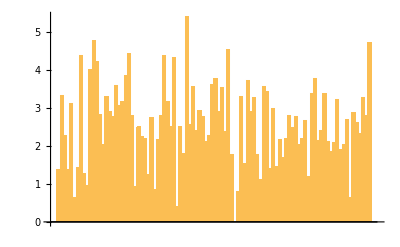

```mathematica
BarChart[nums]
```

```mathematica
Tally[Table[RandomChoice[{0,1,2}], 10]]
```

{{2,5},{0,4},{1,1}}

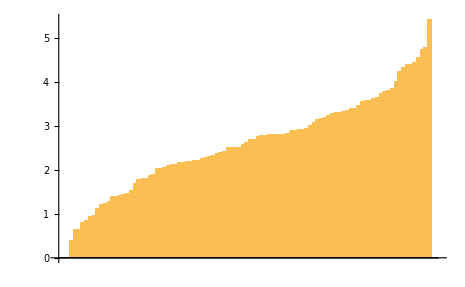

```mathematica
BarChart[Tooltip@@@Reverse[bs,2]]
```

```mathematica
Tally[Table[RandomChoice[{0,1,2}], 10]]
```

{{1,5},{0,1},{2,4}}

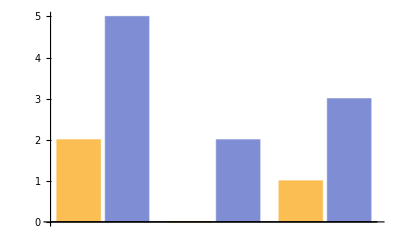

```mathematica
BarChart[%]
```

```mathematica
ResourceFunction["DarkMode"][False]
```

## Experimenting 2

```mathematica
states = Map[#[EntityProperty["AdministrativeDivision","StateAbbreviation"]]&,EntityList[EntityClass["AdministrativeDivision","AllUSStatesPlusDC"]]]
```

{AL,AK,AZ,AR,CA,CO,CT,DE,DC,FL,GA,HI,ID,IL,IN,IA,KS,KY,LA,ME,MD,MA,MI,MN,MS,MO,MT,NE,NV,NH,NJ,NM,NY,NC,ND,OH,OK,OR,PA,RI,SC,SD,TN,TX,UT,VT,VA,WA,WV,WI,WY}

```mathematica
stateLinks = Import["https://publicreporting.sts.org/chsd?title=&field_state_value=NY", "Hyperlinks"]
```

```mathematica
stateFacLinks = Select[stateLinks, StringContainsQ[#, "congenital"]&]
```

```mathematica
stateXML  =  Import["https://publicreporting.sts.org/chsd?title=&field_state_value=NY", "XMLObject"];
```

```mathematica
stateLocXML = Cases[stateXML,  XMLElement["div",{"class"->"search--location"},{_String}],  Infinity]
```

```mathematica
locs = (Last[Last[#1]] & ) /@ stateLocXML
```

{Albany, New York,New Hyde Park, New York,New York, New York,New York, New York,New York, New York,New York, New York,Rochester, New York}

```mathematica
getStateLink[state_]:= Module[{stateLinks,conLinks,xml,locXML,locs},
stateLinks = Import["https://publicreporting.sts.org/chsd?title=&field_state_value="<>state,"Hyperlinks"];
Pause[1];
conLinks = Select[stateLinks, StringContainsQ[#1,"congenital"]&];
xml  =  Import["https://publicreporting.sts.org/chsd?title=&field_state_value="<>state, "XMLObject"];
locXML = Cases[xml,  XMLElement["div",{"class"->"search--location"},{_String}],  Infinity];
locs = (Last[Last[#1]] & ) /@ locXML;
{conLinks, locs}
]
```

```mathematica
ny = getStateLink["NY"]
```

{{https://publicreporting.sts.org/congenital/50127,https://publicreporting.sts.org/congenital/50119,https://publicreporting.sts.org/congenital/50075,https://publicreporting.sts.org/congenital/50063,https://publicreporting.sts.org/congenital/50097,https://publicreporting.sts.org/congenital/50006,https://publicreporting.sts.org/congenital/50082},{Albany, New York,New Hyde Park, New York,New York, New York,New York, New York,New York, New York,New York, New York,Rochester, New York}}

```mathematica
dc = getStateLink["DC"]
```

{{https://publicreporting.sts.org/congenital/50107},{Washington, District of Columbia}}

```mathematica
linksAndLocs = getStateLink /@ states
```

{{{https://publicreporting.sts.org/index.php/congenital/50087},{Birmingham, Alabama}},{{},{}},{{https://publicreporting.sts.org/congenital/50102},{Phoenix, Arizona}},{{https://publicreporting.sts.org/congenital/50050},{Little Rock, Arkansas}},{{https://publicreporting.sts.org/congenital/50110,https://publicreporting.sts.org/congenital/50016,https://publicreporting.sts.org/congenital/50025,https://publicreporting.sts.org/congenital/50004,https://publicreporting.sts.org/congenital/50106,https://publicreporting.sts.org/congenital/50158,https://publicreporting.sts.org/congenital/50008,https://publicreporting.sts.org/congenital/50059,https://publicreporting.sts.org/congenital/50109,https://publicreporting.sts.org/congenital/50080,https://publicreporting.sts.org/congenital/50134},{Los Angeles, California,Los Angeles, California,Orange, California,Loma Linda, California,Stanford, California,Long Beach, California,San Diego, California,Sacramento, California,Sacramento, California,Los Angeles, California,San Francisco, California}},{{https://publicreporting.sts.org/congenital/50009},{Aurora, Colorado}},{{https://publicreporting.sts.org/congenital/50142,https://publicreporting.sts.org/congenital/50074},{Hartford, Connecticut,New Haven, Connecticut}},{{https://publicreporting.sts.org/congenital/50067},{Wilmington, Delaware}},{{https://publicreporting.sts.org/congenital/50107},{Washington, District of Columbia}},{{https://publicreporting.sts.org/congenital/50049,https://publicreporting.sts.org/index.php/congenital/50140,https://publicreporting.sts.org/index.php/congenital/50039,https://publicreporting.sts.org/index.php/congenital/50070,https://publicreporting.sts.org/index.php/congenital/51007,https://publicreporting.sts.org/congenital/50157,https://publicreporting.sts.org/congenital/50003,https://publicreporting.sts.org/congenital/50148,https://publicreporting.sts.org/congenital/50038,https://publicreporting.sts.org/congenital/50044},{Orlando, Florida,Orlando, Florida,Miami, Florida,Hollywood, Florida,St. Petersburg, Florida,Orlando, Florida,Miami, Florida,Tampa, Florida,Gainesville, Florida,Jacksonville, Florida}},{{https://publicreporting.sts.org/congenital/50001},{Atlanta, Georgia}},{{https://publicreporting.sts.org/congenital/50101},{Honolulu, Hawaii}},{{},{}},{{https://publicreporting.sts.org/congenital/50150,https://publicreporting.sts.org/congenital/50005},{Oak Lawn, Illinois,Chicago, Illinois}},{{https://publicreporting.sts.org/congenital/50156,https://publicreporting.sts.org/congenital/50104},{Indianapolis, Indiana,Indianapolis, Indiana}},{{https://publicreporting.sts.org/congenital/50079},{Iowa City, Iowa}},{{},{}},{{https://publicreporting.sts.org/congenital/50062,https://publicreporting.sts.org/congenital/50108},{Louisville, Kentucky,Lexington, Kentucky}},{{https://publicreporting.sts.org/congenital/50098,https://publicreporting.sts.org/congenital/50041},{New Orleans, Louisiana,New Orleans, Louisiana}},{{https://publicreporting.sts.org/congenital/50014},{Portland, Maine}},{{https://publicreporting.sts.org/congenital/50020,https://publicreporting.sts.org/congenital/50129},{Baltimore, Maryland,Baltimore, Maryland}},{{https://publicreporting.sts.org/congenital/50054},{Boston, Massachusetts}},{{https://publicreporting.sts.org/congenital/50065,https://publicreporting.sts.org/congenital/50024,https://publicreporting.sts.org/index.php/congenital/50022},{Ann Arbor, Michigan,Detroit, Michigan,Grand Rapids, Michigan}},{{https://publicreporting.sts.org/congenital/51002,https://publicreporting.sts.org/congenital/50135},{Rochester, Minnesota,Minneapolis, Minnesota}},{{https://publicreporting.sts.org/congenital/50099},{Jackson, Mississippi}},{{https://publicreporting.sts.org/congenital/50132,https://publicreporting.sts.org/congenital/50078,https://publicreporting.sts.org/congenital/50083},{St. Louis, Missouri,St. Louis, Missouri,Kansas City, Missouri}},{{},{}},{{https://publicreporting.sts.org/congenital/50017},{Omaha, Nebraska}},{{https://publicreporting.sts.org/index.php/congenital/50137},{Las Vegas, Nevada}},{{},{}},{{https://publicreporting.sts.org/congenital/50161},{Newark, New Jersey}},{{},{}},{{https://publicreporting.sts.org/congenital/50127,https://publicreporting.sts.org/congenital/50119,https://publicreporting.sts.org/congenital/50075,https://publicreporting.sts.org/congenital/50063,https://publicreporting.sts.org/congenital/50097,https://publicreporting.sts.org/congenital/50006,https://publicreporting.sts.org/congenital/50082},{Albany, New York,New Hyde Park, New York,New York, New York,New York, New York,New York, New York,New York, New York,Rochester, New York}},{{https://publicreporting.sts.org/congenital/50081,https://publicreporting.sts.org/congenital/50064,https://publicreporting.sts.org/congenital/50045,https://publicreporting.sts.org/congenital/50121},{Charlotte, North Carolina,Durham, North Carolina,Chapel Hill, North Carolina,Winston Salem, North Carolina}},{{},{}},{{https://publicreporting.sts.org/congenital/50023,https://publicreporting.sts.org/index.php/congenital/50010,https://publicreporting.sts.org/index.php/congenital/50092,https://publicreporting.sts.org/congenital/50021,https://publicreporting.sts.org/congenital/50015},{Akron, Ohio,Cincinnati, Ohio,Cleveland, Ohio,Columbus, Ohio,Cleveland, Ohio}},{{https://publicreporting.sts.org/congenital/50068},{Oklahoma City, Oklahoma}},{{https://publicreporting.sts.org/congenital/50057,https://publicreporting.sts.org/congenital/50094},{Portland, Oregon,Portland, Oregon}},{{https://publicreporting.sts.org/congenital/50007,https://publicreporting.sts.org/congenital/50051,https://publicreporting.sts.org/congenital/50012,https://publicreporting.sts.org/congenital/50071},{Philadelphia, Pennsylvania,Pittsburgh, Pennsylvania,Danville, Pennsylvania,Hershey, Pennsylvania}},{{},{}},{{https://publicreporting.sts.org/congenital/50072},{Charleston, South Carolina}},{{},{}},{{https://publicreporting.sts.org/congenital/50095,https://publicreporting.sts.org/congenital/50073},{Memphis, Tennessee,Nashville, Tennessee}},{{https://publicreporting.sts.org/congenital/50117,https://publicreporting.sts.org/congenital/50146,https://publicreporting.sts.org/congenital/50114,https://publicreporting.sts.org/congenital/50037,https://publicreporting.sts.org/congenital/50042,https://publicreporting.sts.org/congenital/50133,https://publicreporting.sts.org/congenital/50048,https://publicreporting.sts.org/congenital/50060,https://publicreporting.sts.org/congenital/50089},{Dallas, Texas,San Antonio, Texas,Houston, Texas,Fort Worth, Texas,Austin, Texas,Corpus Christi, Texas,Dallas, Texas,Houston, Texas,San Antonio, Texas}},{{https://publicreporting.sts.org/congenital/50090},{Salt Lake City, Utah}},{{},{}},{{https://publicreporting.sts.org/congenital/51112,https://publicreporting.sts.org/congenital/50086,https://publicreporting.sts.org/congenital/50077,https://publicreporting.sts.org/congenital/50036},{Richmond, Virginia,Norfolk, Virginia,Falls Church, Virginia,Charlottesville, Virginia}},{{https://publicreporting.sts.org/congenital/50046,https://publicreporting.sts.org/index.php/congenital/50126},{Spokane, Washington,Seattle, Washington}},{{https://publicreporting.sts.org/index.php/congenital/50124},{Morgantown, West Virginia}},{{https://publicreporting.sts.org/congenital/50069,https://publicreporting.sts.org/congenital/50056},{Madison, Wisconsin,Milwaukee, Wisconsin}},{{},{}}}

```mathematica
TableForm[linksAndLocs]
```

https://publicreporting.sts.org/index.php/congenital/50087 | Birmingham, Alabama
 | 
https://publicreporting.sts.org/congenital/50102 | Phoenix, Arizona
https://publicreporting.sts.org/congenital/50050 | Little Rock, Arkansas
https://publicreporting.sts.org/congenital/50110
https://publicreporting.sts.org/congenital/50016
https://publicreporting.sts.org/congenital/50025
https://publicreporting.sts.org/congenital/50004
https://publicreporting.sts.org/congenital/50106
https://publicreporting.sts.org/congenital/50158
https://publicreporting.sts.org/congenital/50008
https://publicreporting.sts.org/congenital/50059
https://publicreporting.sts.org/congenital/50109
https://publicreporting.sts.org/congenital/50080
https://publicreporting.sts.org/congenital/50134 | Los Angeles, California
Los Angeles, California
Orange, California
Loma Linda, California
Stanford, California
Long Beach, California
San Diego, California
Sacramento, California
Sacramento, California
Los Angeles, California
San Francisco, California
https://publicreporting.sts.org/congenital/50009 | Aurora, Colorado
https://publicreporting.sts.org/congenital/50142
https://publicreporting.sts.org/congenital/50074 | Hartford, Connecticut
New Haven, Connecticut
https://publicreporting.sts.org/congenital/50067 | Wilmington, Delaware
https://publicreporting.sts.org/congenital/50107 | Washington, District of Columbia
https://publicreporting.sts.org/congenital/50049
https://publicreporting.sts.org/index.php/congenital/50140
https://publicreporting.sts.org/index.php/congenital/50039
https://publicreporting.sts.org/index.php/congenital/50070
https://publicreporting.sts.org/index.php/congenital/51007
https://publicreporting.sts.org/congenital/50157
https://publicreporting.sts.org/congenital/50003
https://publicreporting.sts.org/congenital/50148
https://publicreporting.sts.org/congenital/50038
https://publicreporting.sts.org/congenital/50044 | Orlando, Florida
Orlando, Florida
Miami, Florida
Hollywood, Florida
St. Petersburg, Florida
Orlando, Florida
Miami, Florida
Tampa, Florida
Gainesville, Florida
Jacksonville, Florida
https://publicreporting.sts.org/congenital/50001 | Atlanta, Georgia
https://publicreporting.sts.org/congenital/50101 | Honolulu, Hawaii
 | 
https://publicreporting.sts.org/congenital/50150
https://publicreporting.sts.org/congenital/50005 | Oak Lawn, Illinois
Chicago, Illinois
https://publicreporting.sts.org/congenital/50156
https://publicreporting.sts.org/congenital/50104 | Indianapolis, Indiana
Indianapolis, Indiana
https://publicreporting.sts.org/congenital/50079 | Iowa City, Iowa
 | 
https://publicreporting.sts.org/congenital/50062
https://publicreporting.sts.org/congenital/50108 | Louisville, Kentucky
Lexington, Kentucky
https://publicreporting.sts.org/congenital/50098
https://publicreporting.sts.org/congenital/50041 | New Orleans, Louisiana
New Orleans, Louisiana
https://publicreporting.sts.org/congenital/50014 | Portland, Maine
https://publicreporting.sts.org/congenital/50020
https://publicreporting.sts.org/congenital/50129 | Baltimore, Maryland
Baltimore, Maryland
https://publicreporting.sts.org/congenital/50054 | Boston, Massachusetts
https://publicreporting.sts.org/congenital/50065
https://publicreporting.sts.org/congenital/50024
https://publicreporting.sts.org/index.php/congenital/50022 | Ann Arbor, Michigan
Detroit, Michigan
Grand Rapids, Michigan
https://publicreporting.sts.org/congenital/51002
https://publicreporting.sts.org/congenital/50135 | Rochester, Minnesota
Minneapolis, Minnesota
https://publicreporting.sts.org/congenital/50099 | Jackson, Mississippi
https://publicreporting.sts.org/congenital/50132
https://publicreporting.sts.org/congenital/50078
https://publicreporting.sts.org/congenital/50083 | St. Louis, Missouri
St. Louis, Missouri
Kansas City, Missouri
 | 
https://publicreporting.sts.org/congenital/50017 | Omaha, Nebraska
https://publicreporting.sts.org/index.php/congenital/50137 | Las Vegas, Nevada
 | 
https://publicreporting.sts.org/congenital/50161 | Newark, New Jersey
 | 
https://publicreporting.sts.org/congenital/50127
https://publicreporting.sts.org/congenital/50119
https://publicreporting.sts.org/congenital/50075
https://publicreporting.sts.org/congenital/50063
https://publicreporting.sts.org/congenital/50097
https://publicreporting.sts.org/congenital/50006
https://publicreporting.sts.org/congenital/50082 | Albany, New York
New Hyde Park, New York
New York, New York
New York, New York
New York, New York
New York, New York
Rochester, New York
https://publicreporting.sts.org/congenital/50081
https://publicreporting.sts.org/congenital/50064
https://publicreporting.sts.org/congenital/50045
https://publicreporting.sts.org/congenital/50121 | Charlotte, North Carolina
Durham, North Carolina
Chapel Hill, North Carolina
Winston Salem, North Carolina
 | 
https://publicreporting.sts.org/congenital/50023
https://publicreporting.sts.org/index.php/congenital/50010
https://publicreporting.sts.org/index.php/congenital/50092
https://publicreporting.sts.org/congenital/50021
https://publicreporting.sts.org/congenital/50015 | Akron, Ohio
Cincinnati, Ohio
Cleveland, Ohio
Columbus, Ohio
Cleveland, Ohio
https://publicreporting.sts.org/congenital/50068 | Oklahoma City, Oklahoma
https://publicreporting.sts.org/congenital/50057
https://publicreporting.sts.org/congenital/50094 | Portland, Oregon
Portland, Oregon
https://publicreporting.sts.org/congenital/50007
https://publicreporting.sts.org/congenital/50051
https://publicreporting.sts.org/congenital/50012
https://publicreporting.sts.org/congenital/50071 | Philadelphia, Pennsylvania
Pittsburgh, Pennsylvania
Danville, Pennsylvania
Hershey, Pennsylvania
 | 
https://publicreporting.sts.org/congenital/50072 | Charleston, South Carolina
 | 
https://publicreporting.sts.org/congenital/50095
https://publicreporting.sts.org/congenital/50073 | Memphis, Tennessee
Nashville, Tennessee
https://publicreporting.sts.org/congenital/50117
https://publicreporting.sts.org/congenital/50146
https://publicreporting.sts.org/congenital/50114
https://publicreporting.sts.org/congenital/50037
https://publicreporting.sts.org/congenital/50042
https://publicreporting.sts.org/congenital/50133
https://publicreporting.sts.org/congenital/50048
https://publicreporting.sts.org/congenital/50060
https://publicreporting.sts.org/congenital/50089 | Dallas, Texas
San Antonio, Texas
Houston, Texas
Fort Worth, Texas
Austin, Texas
Corpus Christi, Texas
Dallas, Texas
Houston, Texas
San Antonio, Texas
https://publicreporting.sts.org/congenital/50090 | Salt Lake City, Utah
 | 
https://publicreporting.sts.org/congenital/51112
https://publicreporting.sts.org/congenital/50086
https://publicreporting.sts.org/congenital/50077
https://publicreporting.sts.org/congenital/50036 | Richmond, Virginia
Norfolk, Virginia
Falls Church, Virginia
Charlottesville, Virginia
https://publicreporting.sts.org/congenital/50046
https://publicreporting.sts.org/index.php/congenital/50126 | Spokane, Washington
Seattle, Washington
https://publicreporting.sts.org/index.php/congenital/50124 | Morgantown, West Virginia
https://publicreporting.sts.org/congenital/50069
https://publicreporting.sts.org/congenital/50056 | Madison, Wisconsin
Milwaukee, Wisconsin
 |